```mathematica
(*importar dados do excel*)
```

```mathematica
s=Import["C:\\Users\\Utilizador\\Desktop\\data10.csv"];
```

```mathematica
(*ler dados: campo magnetico (cx,cy,cz) e dados orbitais*)
```

```mathematica
length=5369;
```

```mathematica
Do[cx[i]=s[[i,1]],{i,1,length}]
```

```mathematica
Do[cy[i]=s[[i,2]],{i,1,length}]
```

```mathematica
Do[cz[i]=s[[i,3]],{i,1,length}]
```

```mathematica
Do[lat[i]=s[[i,4]]*Pi/180,{i,1,length}]
```

```mathematica
Do[lon[i]=s[[i,5]]*Pi/180,{i,1,length}]
```

```mathematica
Do[alt[i]=s[[i,6]]/1000000,{i,1,length}]
```

```mathematica
(*cálculo da distancia ao centro da terra a partir da altitude*)
```

```mathematica
a=6.378137;
```

```mathematica
b=6.356752314245;
```

```mathematica
Do[ss[i]=a^2/Sqrt[a^2*Cos[lat[i]]^2+b^2*Sin[lat[i]]^2],{i,1,length}]
```

```mathematica
(*cálculo de z (norte), x e y (x aponta na direcao do meridiano de greenwich)*)
```

```mathematica
Do[x[i]=(alt[i]+ss[i])*Cos[lat[i]]*Cos[lon[i]],{i,1,length}]
```

```mathematica
Do[y[i]=(alt[i]+ss[i])*Cos[lat[i]]*Sin[lon[i]],{i,1,length}]
```

```mathematica
Do[z[i]=(alt[i]+ss[i])*Sin[lat[i]],{i,1,length}]
```

```mathematica
(*modulo do campo magnetico*)
```

```mathematica
Do[mc[i]=Sqrt[cx[i]^2+cy[i]^2+cz[i]^2],{i,1,length}]
```

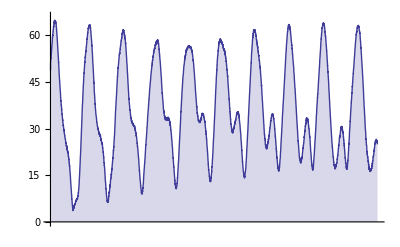

```mathematica
DiscretePlot[mc[i],{i,1,length},Ticks->{None,Automatic},PlotRange->{0,66}]
```

```mathematica
(*campo previsto pelo modelo dipolar*)
```

```mathematica
bx[mx_,my_,mz_,xx_,yy_,zz_,i_]:=1000*(3*(mx*(x[i]-xx)+my*(y[i]-yy)+mz*(z[i]-zz))*(x[i]-xx)/Sqrt[(x[i]-xx)^2+(y[i]-yy)^2+(z[i]-zz)^2]^5-mx/Sqrt[(x[i]-xx)^2+(y[i]-yy)^2+(z[i]-zz)^2]^3)
```

```mathematica
by[mx_,my_,mz_,xx_,yy_,zz_,i_]:=1000*(3*(mx*(x[i]-xx)+my*(y[i]-yy)+mz*(z[i]-zz))*(y[i]-yy)/Sqrt[(x[i]-xx)^2+(y[i]-yy)^2+(z[i]-zz)^2]^5-my/Sqrt[(x[i]-xx)^2+(y[i]-yy)^2+(z[i]-zz)^2]^3)
```

```mathematica
bz[mx_,my_,mz_,xx_,yy_,zz_,i_]:=1000*(3*(mx*(x[i]-xx)+my*(y[i]-yy)+mz*(z[i]-zz))*(z[i]-zz)/Sqrt[(x[i]-xx)^2+(y[i]-yy)^2+(z[i]-zz)^2]^5-mz/Sqrt[(x[i]-xx)^2+(y[i]-yy)^2+(z[i]-zz)^2]^3)
```

```mathematica
(*calculo das coordenadas dos polos magneticos*)
```

```mathematica
pn=a^2/Sqrt[a^2*Cos[80.37*Pi/180]^2+b^2*Sin[80.37*Pi/180]^2]*{Cos[80.37*Pi/180]*Cos[(180-72.62)*Pi/180],Cos[80.37*Pi/180]*Sin[(180-72.62)*Pi/180],Sin[80.37*Pi/180]};
```

```mathematica
ps=a^2/Sqrt[a^2*Cos[-79.74*Pi/180]^2+b^2*Sin[-79.74*Pi/180]^2]*{Cos[-79.74*Pi/180]*Cos[(180+108.22)*Pi/180],Cos[-79.74*Pi/180]*Sin[(180+108.22)*Pi/180],Sin[-79.74*Pi/180]};
```

```mathematica
(*calculo do momento magnetico e do seu desvio do centro da terra a partir das coordenadas dos polos*)
```

```mathematica
m=-7.95*(pn-ps)/Sqrt[(pn-ps).(pn-ps)];
```

```mathematica
r=pn.(pn-ps)/(pn-ps).(pn-ps)*ps+ps.(ps-pn)/(pn-ps).(pn-ps)*pn;
```

```mathematica
(*campo magnetico previsto na aproximacao dipolar*)
```

```mathematica
tbx=Table[1000*(3*(m[[1]]*(x[i]-r[[1]])+m[[2]]*(y[i]-r[[2]])+m[[3]]*(z[i]-r[[3]]))*(x[i]-r[[1]])/Sqrt[(x[i]-r[[1]])^2+(y[i]-r[[2]])^2+(z[i]-r[[3]])^2]^5-m[[1]]/Sqrt[(x[i]-r[[1]])^2+(y[i]-r[[2]])^2+(z[i]-r[[3]])^2]^3),{i,1,length}];
```

```mathematica
tby=Table[1000*(3*(m[[1]]*(x[i]-r[[1]])+m[[2]]*(y[i]-r[[2]])+m[[3]]*(z[i]-r[[3]]))*(y[i]-r[[2]])/Sqrt[(x[i]-r[[1]])^2+(y[i]-r[[2]])^2+(z[i]-r[[3]])^2]^5-m[[2]]/Sqrt[(x[i]-r[[1]])^2+(y[i]-r[[2]])^2+(z[i]-r[[3]])^2]^3),{i,1,length}];
```

```mathematica
tbz=Table[1000*(3*(m[[1]]*(x[i]-r[[1]])+m[[2]]*(y[i]-r[[2]])+m[[3]]*(z[i]-r[[3]]))*(z[i]-r[[3]])/Sqrt[(x[i]-r[[1]])^2+(y[i]-r[[2]])^2+(z[i]-r[[3]])^2]^5-m[[3]]/Sqrt[(x[i]-r[[1]])^2+(y[i]-r[[2]])^2+(z[i]-r[[3]])^2]^3),{i,1,length}];
```

```mathematica
(*modulo do campo na aproximacao dipolar*)
```

```mathematica
tmb=Table[Sqrt[tbx[[i]]^2+tby[[i]]^2+tbz[[i]]^2],{i,1,length}];
```

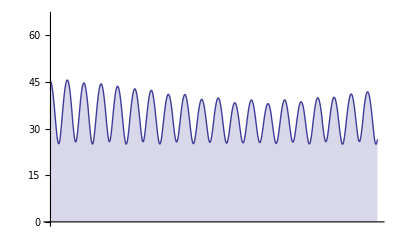

```mathematica
DiscretePlot[tmb[[i]],{i,1,length},Ticks->{None,Automatic},PlotRange->{0,66}]
```

```mathematica
(*leitura de momentos multipolares do excel*)
```

```mathematica
mg=Import["C:\\Users\\Utilizador\\Desktop\\wmg.csv"];
```

```mathematica
mh=Import["C:\\Users\\Utilizador\\Desktop\\wmh.csv"];
```

```mathematica
(*construcao das matrizes dos momentos multipolares*)
```

```mathematica
h=Table[0,{i,13},{j,1,14}];
```

```mathematica
g=Table[0,{i,13},{j,1,14}];
```

```mathematica
Do[g[[i,j]]=mg[[i*(i+1)/2-1+j]][[1]],{i,1,13},{j,1,i+1}]
```

```mathematica
Do[h[[i,j]]=mh[[i*(i+1)/2-1+j]][[1]],{i,1,13},{j,1,i+1}]
```

```mathematica
(*raio da terra no modelo multipolar e ordem da expansao*)
```

```mathematica
rt=6.3712;
```

```mathematica
n=13;
```

```mathematica
(*campo no modelo multipolar*)
```

```mathematica
V[r_,la_,lo_]:=rt*Sum[(rt/r)^(i+1)*(g[[i,j]]*Cos[(j-1)*lo]+h[[i,j]]*Sin[(j-1)*lo])*LegendreP[i,j-1,Sin[la]]*(-1)^(j-1)*Sqrt[(2-KroneckerDelta[j,1])*(i-j+1)!/(i+j-1)!],{i,1,n},{j,1,i+1}]/1000
```

```mathematica
dvr[r_,la_,lo_]:=D[V[x,la,lo],x]/.x->r
```

```mathematica
dvla[r_,la_,lo_]:=D[V[r,x,lo],x]/r/.x->la
```

```mathematica
dvlo[r_,la_,lo_]:=D[V[r,la,x],x]/r/Cos[la]/.x->lo
```

```mathematica
Bx[r_,la_,lo_]:=(-Cos[la]*dvr[r,la,lo]+Sin[la]*dvla[r,la,lo])*Cos[lo]+Sin[lo]*dvlo[r,la,lo]
```

```mathematica
By[r_,la_,lo_]:=(-Cos[la]*dvr[r,la,lo]+Sin[la]*dvla[r,la,lo])*Sin[lo]-Cos[lo]*dvlo[r,la,lo]
```

```mathematica
Bz[r_,la_,lo_]:=-Sin[la]*dvr[r,la,lo]-Cos[la]*dvla[r,la,lo]
```

```mathematica
(*modulo do campo no modelo multipolar*)
```

```mathematica
B[r_,la_,lo_]:=Sqrt[Bx[r,la,lo]^2+By[r,la,lo]^2+Bz[r,la,lo]^2]
```

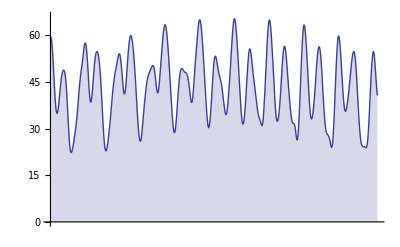

```mathematica
DiscretePlot[B[ss[i],lat[i],lon[i]],{i,1,length},Ticks->{None,Automatic},PlotRange->{0,66}]
```

```mathematica
(*campo no referencial da ISS*)
```

```mathematica
bbx[mx_,my_,mz_,xx_,yy_,zz_,i_]:=((x[i]*x[i-1]+y[i]*y[i-1]+z[i]*z[i-1])*(bx[mx,my,mz,xx,yy,zz,i]*x[i]+by[mx,my,mz,xx,yy,zz,i]*y[i]+bz[mx,my,mz,xx,yy,zz,i]*z[i])-(x[i]^2+y[i]^2+z[i]^2)*(bx[mx,my,mz,xx,yy,zz,i]*x[i-1]+by[mx,my,mz,xx,yy,zz,i]*y[i-1]+bz[mx,my,mz,xx,yy,zz,i]*z[i-1]))/Sqrt[x[i]^2+y[i]^2+z[i]^2]/Sqrt[(y[i]*z[i-1]-z[i]*y[i-1])^2+(z[i]*x[i-1]-x[i]*z[i-1])^2+(x[i]*y[i-1]-y[i]*x[i-1])^2]
```

```mathematica
bby[mx_,my_,mz_,xx_,yy_,zz_,i_]:=(bx[mx,my,mz,xx,yy,zz,i]*x[i]+by[mx,my,mz,xx,yy,zz,i]*y[i]+bz[mx,my,mz,xx,yy,zz,i]*z[i])/Sqrt[x[i]^2+y[i]^2+z[i]^2]
```

```mathematica
bbz[mx_,my_,mz_,xx_,yy_,zz_,i_]:=(bx[mx,my,mz,xx,yy,zz,i]*(y[i]*z[i-1]-z[i]*y[i-1])+by[mx,my,mz,xx,yy,zz,i]*(z[i]*x[i-1]-x[i]*z[i-1])+bz[mx,my,mz,xx,yy,zz,i]*(x[i]*y[i-1]-y[i]*x[i-1]))/Sqrt[(y[i]*z[i-1]-z[i]*y[i-1])^2+(z[i]*x[i-1]-x[i]*z[i-1])^2+(x[i]*y[i-1]-y[i]*x[i-1])^2]
```

```mathematica
(*campo no referencial do raspberry*)
```

```mathematica
ba[mx_,my_,mz_,xx_,yy_,zz_,al_,be_,ga_,i_]:=Cos[al]*Cos[be]*bbx[mx,my,mz,xx,yy,zz,i]+(Cos[al]*Sin[be]*Sin[ga]-Sin[al]*Cos[ga])*bby[mx,my,mz,xx,yy,zz,i]+(Cos[al]*Sin[be]*Cos[ga]+Sin[al]*Sin[ga])*bbz[mx,my,mz,xx,yy,zz,i]
```

```mathematica
bb[mx_,my_,mz_,xx_,yy_,zz_,al_,be_,ga_,i_]:=Sin[al]*Cos[be]*bbx[mx,my,mz,xx,yy,zz,i]+(Sin[al]*Sin[be]*Sin[ga]+Cos[al]*Cos[ga])*bby[mx,my,mz,xx,yy,zz,i]+(Sin[al]*Sin[be]*Cos[ga]-Cos[al]*Sin[ga])*bbz[mx,my,mz,xx,yy,zz,i]
```

```mathematica
bc[mx_,my_,mz_,xx_,yy_,zz_,al_,be_,ga_,i_]:=-Sin[be]*bbx[mx,my,mz,xx,yy,zz,i]+Cos[be]*Sin[ga]*bby[mx,my,mz,xx,yy,zz,i]+Cos[be]*Cos[ga]*bbz[mx,my,mz,xx,yy,zz,i]
```

```mathematica
(*metodo do minimo da soma dos quadrados*)
```

```mathematica
min[mx_,my_,mz_,xx_,yy_,zz_,al_,be_,ga_]:=Sum[(ba[mx,my,mz,xx,yy,zz,al,be,ga,i]-cx[i])^2+(bb[mx,my,mz,xx,yy,zz,al,be,ga,i]-cy[i])^2+(bc[mx,my,mz,xx,yy,zz,al,be,ga,i]-cz[i])^2,{i,2,length}]
```

```mathematica
(*opcoes do findminimum: WorkingPrecision->16,AccuracyGoal->8,PrecisionGoal->Infinity]*)
```

```mathematica
FindMinimum[min[mx,my,mz,xx,yy,zz,al,be,ga],{{mx,0.42000502581323623},{my,-1.3071303637477159},{mz,-7.830549533108156},{xx,0.018305390575379388},{yy,-0.030515255027940724},{zz,0.00607566202659271},{al,0},{be,0},{ga,0}}]
```

{2.92183×10^6,{mx→-0.404786,my→0.387568,mz→-7.0428,xx→-0.108592,yy→0.280063,zz→0.402186,al→-0.616006,be→0.624256,ga→0.167102}}

```mathematica
(*percentagem de erro*)
```

```mathematica
Sqrt[2.9218315412327005*^6/length]/Sum[mc[i],{i,1,4871}]*length*100
```

71.4594

```mathematica
Sqrt[2.9218315412327005*^6/length/Sum[mc[i]^2,{i,1,4871}]*length]*100
```

62.2995